# research work page

```mathematica
SetDirectory[NotebookDirectory[]];
```

## τ值的推导

### 求解线性方程组

现在先不考虑交换空间.这可以通过假设只研究总内存能够满足分配方案的情况.此时交换空间使用率为0.
即可以满足不用考虑的条件.

原方程组可以重新用矩阵表达:

ΑX=Β

其中Α为(1 | 1 | 1 |   | 1
1 | -1 | 0 | ⋯ | 0
1 | 0 | -1 |   | 0
  | ⋮ |   | ⋱ |  
1 | 0 | 0 |   | -1),Β为(Ν
τ(A_1-A_2)
τ(A_1-A_3)
⋮
τ(A_1-A_n)).n为方程的个数.X=(N_t1
N_t2
N_t3
⋮
N_tn).
现,为了表述方便.左右两边同时除以Ν,使得单位化为1.即Α(X/Ν)=Β/N.
这里需要特别强调.我们约定以下条件.
1.每台虚拟机的初始内存不固定.为物理机内存/虚拟机台数.
2.总内存一直固定为所有物理机内存.
这种设定常常见于实际环境中.为了使利益最大化.希望能够充分使用物理机资源.
解得X为    Α^-1 Β.即

```mathematica
Inverse[({{1, 1, 1, 1}, {1, -1, 0, 0}, {1, 0, -1, 0}, {1, 0, 0, -1}})]//MatrixForm
```

(1/4 | 1/4 | 1/4 | 1/4
1/4 | -3/4 | 1/4 | 1/4
1/4 | 1/4 | -3/4 | 1/4
1/4 | 1/4 | 1/4 | -3/4)

Α^-1 Β=(1/n | 1/n | 1/n |   | 1/n
1/n | 1/n-1 | 1/n | ⋯ | 1/n
1/n | 1/n | 1/n-1 |   | 1/n
  | ⋮ |   | ⋱ |  
1/n | 1/n | 1/n |   | 1/n-1)(1
τ(A_1-A_2)
τ(A_1-A_3)
⋮
τ(A_1-A_n))=(1/n+τ(A_1-1/n∑_(i=1)^n A_i)
1/n+τ(A_2-1/n∑_(i=1)^n A_i)
1/n+τ(A_3-1/n∑_(i=1)^n A_i)
⋮
1/n+τ(A_n-1/n∑_(i=1)^n A_i))

设A=(A_1,A_2,A_3,…,A_n).为整个系统当前使用的内存的向量
其中,当A_i(i=1…n)固定的时候.1/n∑_(i=1)^n A_i为定值.等于Ā.
所以对于N_ti可以重新表述为.所有内存的平均+当前内存和总的使用内存的平均的差值再乘以一个影响系数.
该方程关于τ是一个线性方程.线性变化的.当前内存A_i 和 Ā的差值要么为正要么为负.乘上τ之后都不改变极性.只会改变幅值.
幅度范围以1/n为中心.上下伸展.

### τ的值域的讨论

当0<τ<1时.和τ=1相比实际上是拉小这种差异性.
τ为0的时候.所有解都取得1/n.τ为1的时候差异性最大.
当τ>1时.实际上是拉大这种差异性.但是会因为幅度范围到达负值.也就是一些情况.会分配负的内存.所以是不可取的.
所以τ的取值范围是(0,1]

```mathematica
X[list_List]:=Table[1/Length[list]+τ(list[[i]]-Mean[list]),{i,1,Length[list]}]
```

现在以n=2作出图形,任意取A_1和A_2.(这里取A_1=0,A_2=1)

```mathematica
X2=X[{A1,A2}];
X3=X[{A1,A2,A3}];
```

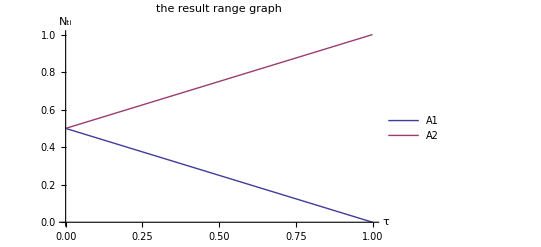

```mathematica
g=Plot[Evaluate[X2/.{A1->0,A2->1}],{τ,0,1},
PlotLabel->"the result range graph",
PlotLegends->{"A1","A2"},AxesLabel->{"τ","N_ti"}]
Export["graph/tau_plot.eps",g];
Export["graph/tau_plot.png",g,ImageResolution->150];
```

可以看出这种变化趋势.

N_ti的求解范围也可以计算出来.可以用一个最大最小值区间来表示.
N_ti的上界即是∀A_i∈[0,1]结果取最大值.由公式可以容易的看出.当A_i=1,A_j=0,j≠i时候N_ti为最大值.N_tj为最小值.
所以可以得到[(1-τ)/n,(1+(n-1)τ)/n]

t

0

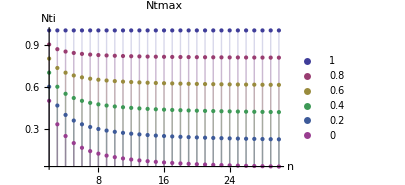
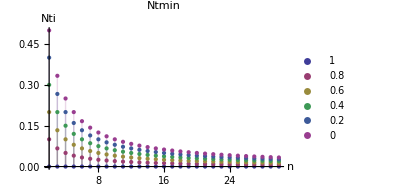

```mathematica
Ntmax[τ_,n_]:=(1+(n-1)τ)/n;
Ntmin[τ_,n_]:=(1-τ)/n;
Limit[Ntmax[t,n],n->Infinity]
Limit[Ntmin[t,n],n->Infinity]
Table[
DiscretePlot[{f[1,n],f[0.8,n],f[0.6,n],f[0.4,n],f[0.2,n],f[0,n]},{n,2,30},
PlotLegends->{1,0.8,0.6,0.4,0.2,0},
AxesLabel->{"n","Nti"},PlotLabel->f,PlotRange->All,
ImageSize->300
]
,{f,{Ntmax,Ntmin}}]//TableForm
```

根据上图.我们可以得到当n→∞时Ntmax→τ,Ntmin→0所以变化区间并不会因为n的增大而缩小.而最后会稳定到[0,τ]区间.这个是比较好的.

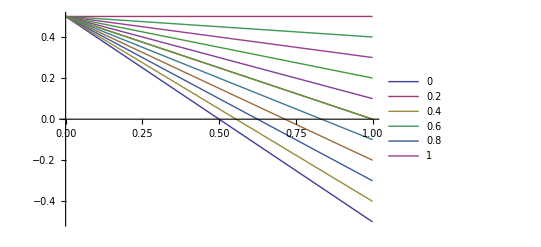
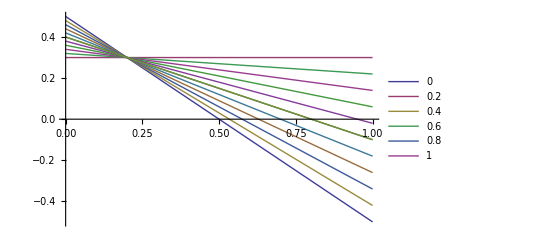
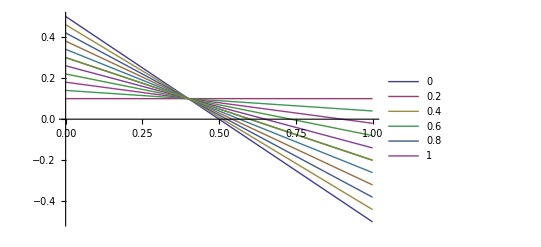
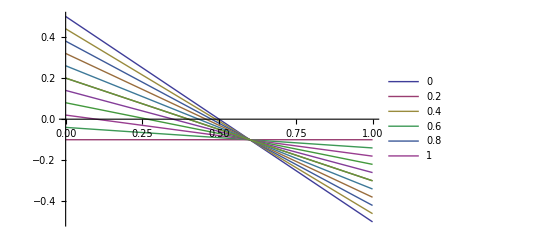
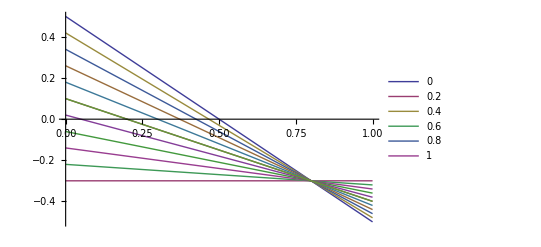

```mathematica
Table[Plot[Evaluate[Table[(X2/.{A1->a,A2->b,τ->t})-{a,b},{t,0,1,0.2}]],{a,0,1},
PlotRange->{{0,1}},
PlotLegends->{"0","0.2","0.4","0.6","0.8","1"}],{b,0,0.8,0.2}]
```

```mathematica
nozero[z_]:=If[z==0,1,z];
tf[l_List]:=(-1/Length[l]+Min[l])/nozero[-Mean[l]+Min[l]]
```

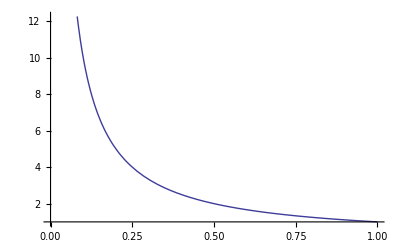

```mathematica
Plot[tf[{a,0}],{a,0,1}]
```

### τ的可行解域的讨论

为了研究不同的τ值的影响.现在我们来从下面一个角度观察.
 >  在总内存能够满足分配的情况下.需要解X的每一个元素N_ti大于等于当前申请的量A_(i.)
 >  也就是分配的结果应该大于申请的容量.
 >  否则.会得出明明还有富余但是分配的反而无法满足提出的需求.这种异常的情况.
所以可以列出条件限制方程组 X≥A 即  Piecewise[{{N_t1≥A_1, □}, {N_t2≥A_2, □}, {⋮, □}, {N_tn≥A_n, □}}]   最后根据τ画出来解区域.称这样的区域为可行解域.
为了方便研究.只画出在n=2时不同τ的可行解域.

```mathematica
Manipulate[RegionPlot[(1/2+(A1+1/2 (-A1-A2)) τ)≥A1&&(1/2+(1/2 (-A1-A2)+A2) τ)≥A2,{A1,0,1},{A2,0,1}],{{τ,0.75},0,2}]
```

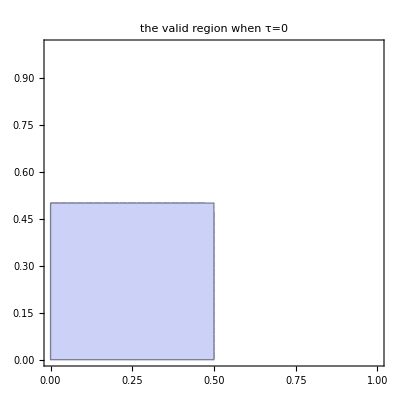

```mathematica
g=RegionPlot[(1/2+(A1+1/2 (-A1-A2)) τ)≥A1&&(1/2+(1/2 (-A1-A2)+A2) τ)≥A2/.τ->0,{A1,0,1},{A2,0,1},
PlotLabel->"the valid region when τ=0"]
Export["graph/valid_region_0.png",g,ImageResolution->150];
```

这个是τ等于0的时候的结果.可以看到.其中满足解的范围非常小.
特别的.总内存为1,每台虚拟机在初始化的时候各自分配0.5.
要求A_1,A_2≤0.5.也就是每台虚拟机只能提出小于等于各自的初始内存.不能超过它.不然解就会违反判定条件.
这个是非常的不合理的.而且是毫无意义的.
下面再看一下τ从0取到1,间隔0.2的情况

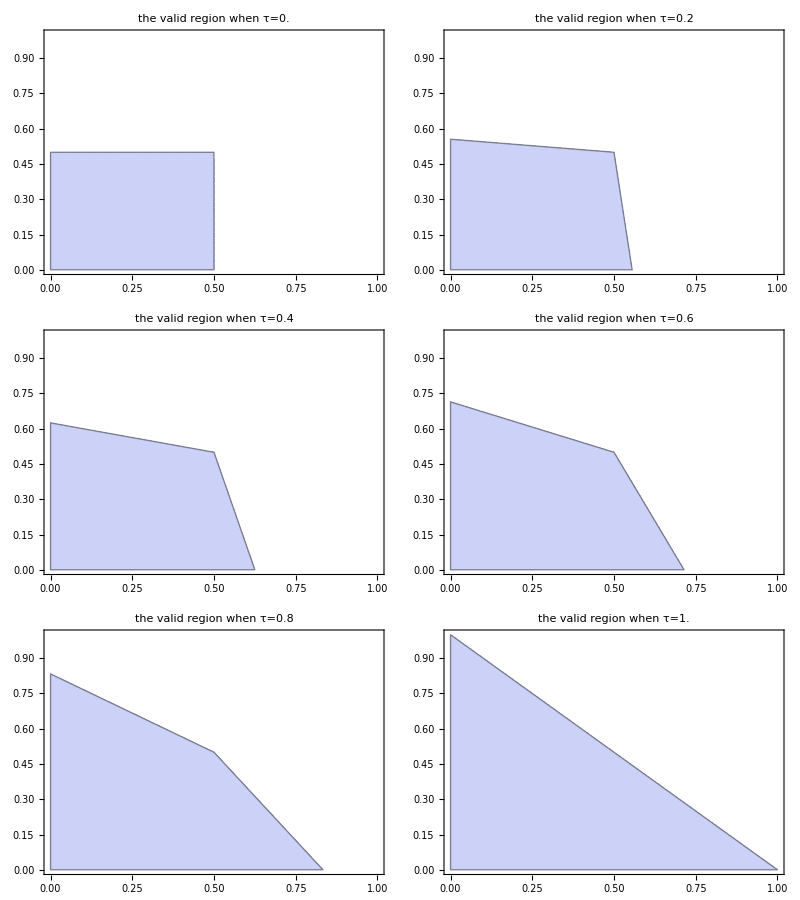

```mathematica
g=Partition[Table[
RegionPlot[(1/2+(A1+1/2 (-A1-A2)) τ)≥A1&&(1/2+(1/2 (-A1-A2)+A2) τ)≥A2,{A1,0,1},{A2,0,1},
PlotLabel->"the valid region when τ="<>ToString[τ]],{τ,0,1,0.2}],2]//TableForm
Export["graph/valid_region_table.png",g,ImageResolution->150];
```

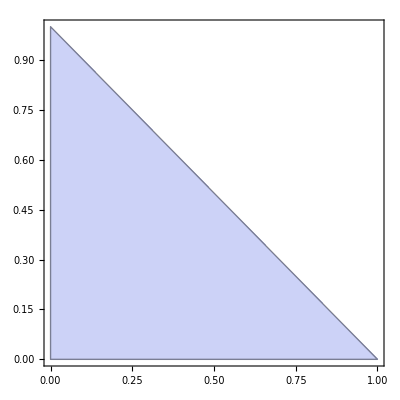

```mathematica
RegionPlot[(1/2+(A1+1/2 (-A1-A2)) tf[{A1,A2}])≥A1&&(1/2+(1/2 (-A1-A2)+A2)  tf[{A1,A2}])≥A2,{A1,0,1},{A2,0,1}]
```

由组图可以看出随着τ的增大.可行解域也不断增大.
具体来说.不可解的例子,如取τ=0.8的图,取A_1=0.8,A_2=0.2.求解得到
X={0.74,0.26}对于A_1就出现了异常解.

当τ为1的时候达到最大,满足可分配条件的全域(A_1+A_2≤1)可解

下面观察一下可行解域随着n的增大的变化情况:

因为n>2时作图就会变得困难.所以有必要重新对公式进行变换.方便研究

对于使用的观测条件.N_ti≥A_i,变换一下可以得到N_ti-A_i=F_i≥0,也就是可用内存大于0.
现在重新计算可用内存F_i=(1/n+τ(A_i-Ā))-A_i=1/n-(1-τ)A_i-τ Ā.
特别的.当τ=1时.有F_i=1/n-Ā.即F_i与i无关.即所有的虚拟机的可用内存均相等为总平均与使用平均的差值.
当Ā=1/n,即∑A=1时.即临界条件:所有使用内存等于总可用内存时候.每台虚拟机的剩余内存为0.
这也是为什么τ=1的可行解域非常大的原因.

但是.考虑到在τ=1时候产生的特殊现象,即所有虚拟机的剩余内存均相等.这感觉有些不公平.

下面,研究可行解域和n的关系.因为当n超过2的时候作图就变得困难了.所以需要变换一种方式.
已知可行解域可以表述为F_i≥0,∀i∈[1...n].也就是所有的虚拟机的可用内存都需要大于0.
所以我们只需要研究其中一台的临界条件.只要它不满足.那么可以知道其他的虚拟机无论是否满足.这整个组合都是不满足条件的.于是有F_i≥0,展开1/n-(1-τ)A_i-τ Ā=1/n-(1-τ)A_i-τ((A_i+A')/n)≥0.我们要重新表述成关于A_i的不等式.
因为Ā和A_i是相关的.所以我们必须把Ā展开成两个部分.A_i和A',其中A'定义为∑A_j(j=1...n,j≠i).
所以现在A'和A_i是无关的了.

```mathematica
Reduce[1/n-(1-t)Ai-t(Ai+A)/n≥0&&t<1&&t>0&&A<1&&A>0&&n>1,Ai]
```

n>1&&0<t<1&&0<A<1&&Ai≤(-1+A t)/(-n-t+n t)

之后可以得到A_i≤(1-τ A')/(n(1-τ)+τ)即为可行解域.它关于A'是线性的.和n=2的作图是符合的.这个不是重点.我们可以画图如下
(A'=0)

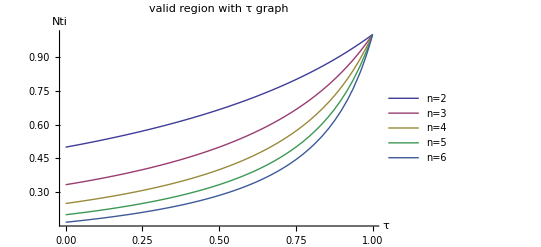

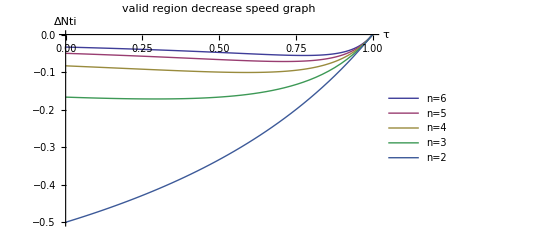

```mathematica
region[n_,τ_,AA_]:=(1-τ AA)/(n(1-τ)+τ);
Plot[Evaluate[Table[region[n,τ,0],{n,2,6}]],{τ,0,1},PlotLegends->{"n=2","n=3","n=4","n=5","n=6"},
AxesLabel->{"τ","Nti"},
PlotLabel->"valid region with τ graph"
]
Plot[Evaluate[Table[region[n,t,0]-region[n-1,t,0],{n,6,2,-1}]],{t,0,1},
PlotLegends->{"n=6","n=5","n=4","n=3","n=2"},
PlotRange->All,
AxesLabel->{"τ","ΔNti"},
PlotLabel->"valid region decrease speed graph"
]
```

这个图我们能够非常直观的发现一个事实.就是除了τ=1之外.其他的τ值导致随着n的增加.
可行解域在不断的缩小.缩小的速度随着n的增加在不断的减小.而且比较有意思的是除了n=2,
在τ比较小的时候.缩小速度是非常相近的.到接近1的时候变化比较快.

公式还可以反解出t>=(-1+A_i n)/(-A+A_i n),因为i是任意的.所以t>=Max[(-1+A_i n)/(-A+A_i n)].

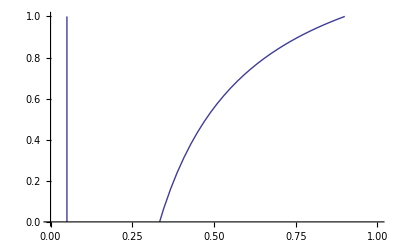

```mathematica
Plot[(1-x n)/(A+x-x n)/.{n->3,A->0.1},{x,0,1},PlotRange->{0,1}]
```

so t=(-1+Max[Ai] n)/(-A+Max[Ai]n)

## ϵ的推导

已知在可行解域之外的时候.就会使用swap分区.此时ϵ项不为0.需要带入重新计算.

### 求解方程组

原来的方程重新写一遍.
((1-τ+ϵ(S1))/(Nt1-τ A1)==(1-τ+ϵ(S2))/(Nt2-τ A2)
(1-τ+ϵ(S1))/(Nt1-τ A1)==(1-τ+ϵ(S3))/(Nt3-τ A3)
⋮
(1-τ+ϵ(S1))/(Nt1-τ A1)==(1-τ+ϵ(Sn))/(Ntn-τ An)
N=∑_(i=1)^n Nt_i
另
T_i=1-τ+ϵS_i
再经过化简和重构.可以得到下面的伪线性方程组
(1 | 1 | 1 | □ | 1
T_2 | -T_1 | □ | ⋯ | □
T_3 | □ | -T_1 | □ | □
□ | ⋮ | □ | ⋱ | □
T_n | □ | □ | □ | -T_1)(Nt_1
Nt_2
Nt_3
⋮
Nt_n)=(N
τ(T_2 A_1-T_1 A_2)
τ(T_3 A_1-T_1 A_3)
□
τ(T_n A_1-T_1 A_n))

```mathematica
LinearSolve[({{1, 1, 1}, {T2, -T1, 0}, {T3, 0, -T1}}),({{1}, {τ(T2 A1-T1 A2)}, {τ(T3 A1-T1 A3)}})]
LinearSolve[({{1, 1, 1, 1}, {T2, -T1, 0, 0}, {T3, 0, -T1, 0}, {T4, 0, 0, -T1}}),({{1}, {τ(T2 A1-T1 A2)}, {τ(T3 A1-T1 A3)}, {τ(T4 A1-T1 A4)}})]
```

{{(T1-A2 T1 τ-A3 T1 τ+A1 T2 τ+A1 T3 τ)/(T1+T2+T3)},{(T2+A2 T1 τ-A1 T2 τ-A3 T2 τ+A2 T3 τ)/(T1+T2+T3)},{(T3+A3 T1 τ+A3 T2 τ-A1 T3 τ-A2 T3 τ)/(T1+T2+T3)}}

{{(T1-A2 T1 τ-A3 T1 τ-A4 T1 τ+A1 T2 τ+A1 T3 τ+A1 T4 τ)/(T1+T2+T3+T4)},{(T2+A2 T1 τ-A1 T2 τ-A3 T2 τ-A4 T2 τ+A2 T3 τ+A2 T4 τ)/(T1+T2+T3+T4)},{(T3+A3 T1 τ+A3 T2 τ-A1 T3 τ-A2 T3 τ-A4 T3 τ+A3 T4 τ)/(T1+T2+T3+T4)},{(T4+A4 T1 τ+A4 T2 τ+A4 T3 τ-A1 T4 τ-A2 T4 τ-A3 T4 τ)/(T1+T2+T3+T4)}}

利用计算机可以求解得到Nt_i=(T_i-T_i τ(∑A_j-A_i)+A_i τ(∑T_j-T_i))/(∑_(j=1)^n T_j)上下同除以n可以再得到(T_i/n-T_i τ Ā+A_i τ T̄)/(T̄)= T_i/(T̄)(1/n-τ Ā)+A_i τ =(1-τ+ϵS_i)/(1-τ+ϵ S̄)(1/n-τ Ā)+A_i τ
当∀S_i=0时.就可以退化成只有τ的简单表达式.而且我们可以看到.和简单表达式相比.含有ϵ的表达式是将1/n-τ Ā这一部分乘以一个权值而且这一部分是和i无关的量,只由虚拟机的整体决定.

=====================not used=============================

```mathematica
f={(1-τ)/(Nt1-τ A1)==(1-τ)/(Nt2-τ A2),Nt1+Nt2==N};
f//TableForm
```

(1-τ)/(Nt1-A1 τ)==(1-τ)/(Nt2-A2 τ)
Nt1+Nt2==N

```mathematica
res=Solve[f,{Nt1,Nt2}]
```

{{Nt1→N/2+(A1 τ)/2-(A2 τ)/2,Nt2→N/2-(A1 τ)/2+(A2 τ)/2}}

```mathematica
Evaluate[res[[1,{1,2},2]]/.N->2]
```

{1+(A1 τ)/2-(A2 τ)/2,1-(A1 τ)/2+(A2 τ)/2}

```mathematica
manu[A1_,A2_,τ_]:=Evaluate[res[[1,{1,2},2]]/.N->2]
```

================================================================================

现在设n=2.作出τ的自变量图形.

```mathematica
Manipulate[ListLinePlot[Table[manu[A1,A2,t],{t,0,1,0.02}]ᵀ,PlotRange->{0,2},PlotLegends->{"A1","A2"}],{{A1,0.5},0,1},{A2,0,1},SaveDefinitions->True]
```

the result for simulate mono test.

```mathematica
Manipulate[ListLinePlot[
(Table[manu[t,a2,0.75],{t,0,1,0.02}]~Join~Table[manu[t,a2,0.75],{t,1,0,-0.02}])ᵀ~Join~{Range[0,1,0.02]~Join~Range[1,0,-0.02]},
PlotLabel->"mono test",PlotRange->{0,1.5},PlotLegends->{"total","free","used"}
],{{a2,0.5},0,1}]
```

the result for simulate random test.

```mathematica
r=RandomReal[1,50];
Manipulate[ListPlot[
manu[#,a2,0.75]&/@rᵀ~Join~{r},Filling->Axis,PlotRange->{0,1.5},PlotLegends->{"total","free","used"}
],{{a2,0.5},0,1},SaveDefinitions->True]
```

```mathematica
t={(1-τ)/(Nt1-τ A1)==(1-τ)/(Nt2-τ A2),(1-τ)/(Nt1-τ A1)==(1-τ)/(Nt3-τ A3),Nt1+Nt2+Nt3==n};
```

```mathematica
t=Solve[t,{Nt1,Nt2,Nt3}];
```

```mathematica
manu3[A1_,A2_,A3_,τ_]:=Evaluate[t[[1,All,2]]/.n->3]
```

```mathematica
Manipulate[ListLinePlot[Table[manu3[A1,A2,A3,τ],{τ,0,1,0.02}]ᵀ,
PlotRange->{0,2},PlotLegends->{"A1","A2","A3"}
],{{A1,0.75},0,1},{{A2,0.5},0,1},{A3,0,1},SaveDefinitions->True]
```

#### the research about τ value.

既然τ是线性变化的.所以在τ表达了一种变化范围的思想.当τ为0时.没有变化.当τ为1.时变化程度最剧烈.
所以可以求得基于τ的最大值和最小值.它们之间就是整个可变范围.

```mathematica
manu[A1,A2,τ]
```

{1+(A1 τ)/2-(A2 τ)/2,1-(A1 τ)/2+(A2 τ)/2}

```mathematica
manu3[A1,A2,A3,tau]//Expand
```

{1+(2 A1 tau)/3-(A2 tau)/3-(A3 tau)/3,1-(A1 tau)/3+(2 A2 tau)/3-(A3 tau)/3,1-(A1 tau)/3-(A2 tau)/3+(2 A3 tau)/3}

当A1取最大,A2取最小时.就可以得到最大值,最小值集合了.再考虑一般解的情况.可以得出
一台虚拟机占用全部内存,其他虚拟机都为0时候就是范围集合.

```mathematica
range[τ_,n_]:={1+(n-1) τ,1-τ }
```

画出图像来

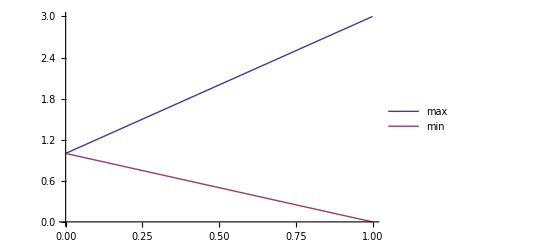

```mathematica
Plot[Evaluate[range[τ,3]],{τ,0,1},PlotLegends->{"max","min"}]
```

其中.非常明显的是,增加虚拟机的台数.只能增加最大值范围.也就是增加上界范围.但是下界范围却和虚拟机台数无关.

现在考虑τ=1的情况,会发现一个比较重要的事实.就是最小值为0.也就是说.可能会有虚拟机完全得不到内存.
在数学意义上.申请内存为0是完全可能的.这个时候理应该给它分配0.但是.事实上.一个运行操作系统的虚拟机不能够分配
0内存.这个和SWAP分区无关.
操作系统运行需要一个最小内存.来存放核心相关的内容.
也就是说要保证一台虚拟机的运行.不能够只是给他分配0内存.然后希望它把所有的运行需要的内存丢到
SWAP分区中.首先不考虑这样带来的巨大的性能损失.重要的是这个是完全不被允许的.
另外一方面.当不断的给一个运行的虚拟机减少分配的总内存的时候.当小于运行最小内存时.系统就会崩溃.造成KernelPanic.
所以虽然在数学意义上τ=1是具有全域可解的很好的性能.但是在这种情况下.会导致过度分配.导致分配0内存.所以需要一个
约束条件来限定它.也就是受保护的最小运行需要内存.作为τ的上界.
其计算公式为τ_up=1-系统最小内存/初始分配内存.因为在上面的计算中.为了简化表达.用1代表每台虚拟机初始分配内存.所以可用的总内存N=n*1.
为了换算成实际内存的MB单位.需要乘以初始内存(一般512~1024M).

```mathematica
tauUp[min_,cur_]:=1-min/cur
```

一般一个系统的最小运行内存和系统有关.运行X的Linux系统典型内存是512MB.现在很多系统要求最小1024MB.
不运行X的Linux服务器系统典型内存是192MB.一般可以分配256MB.
所以可以画出图像来:

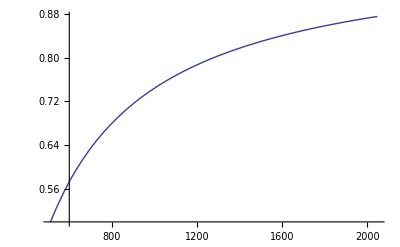

```mathematica
Plot[tauUp[256,m],{m,512,2048}]
```

在典型的初始内存1024MB,最小内存256MB的情况下.τ的上界即为0.75.

总结:通过设置τ为0.75.可以保证在具有尽可能大的可行解域范围的情况下.保护分配的最小内存.从而使得虚拟机能够正常运行.

bug:虽然tau为0.75的时候具有保护策略.但是这个是建立在某一台虚拟机提出申请0内存的情况下.
一般虚拟机正常运行之后,就不可能提出0内存.至少都是最小运行内存.所以提出0这一个条件是永远不可能满足的.
如果真要利用它.可能需要提出保护的最小可用内存.也就是让free memory不能低于某一个值.不过就算低于某一个值.也只是会加剧利用SWAP分区